```mathematica
(x^n+5*x^(n-1))/(x-5)
```

(5 x^(-1+n)+x^n)/(-5+x)

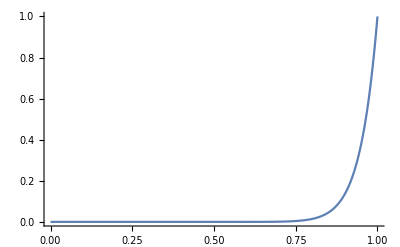

```mathematica
Plot[(5 x^(-1+n)+x^n)/(5+x)/. n-> 16,{x,0,1},PlotRange->{{0,1},All},PlotPoints->Automatic]
```

```mathematica
Clear["Global`*"]
iarray = ConstantArray[0,11];
iarray[[1]] = 0.182321559;
errorarray = ConstantArray[0,11];
For[n=1,n≤10,n+=1,
t= n+1;
iarray[[t]]=n^-1-5*iarray[[t-1]]; 
temp = N[Integrate[x^n/(x+5),{x,0,1}]];
errorarray[[t]]=Abs[ temp-iarray[[t]]]/temp
]

iarray = ConstantArray[0,11];
iarray[[11]] = 0.015367548912763596;
errorarray2 = ConstantArray[0,11];
For[n=10,n≥0,n-=1,
t= n+1;
iarray[[t-1]]=1/5*(n^-1-iarray[[t]]); 
temp = N[Integrate[x^n/(x+5),{x,0,1}]];
errorarray2[[t-1]]=Abs[ temp-iarray[[t-1]]]/temp
]
```

Power::infy: 碰到无穷表达式 1/0.

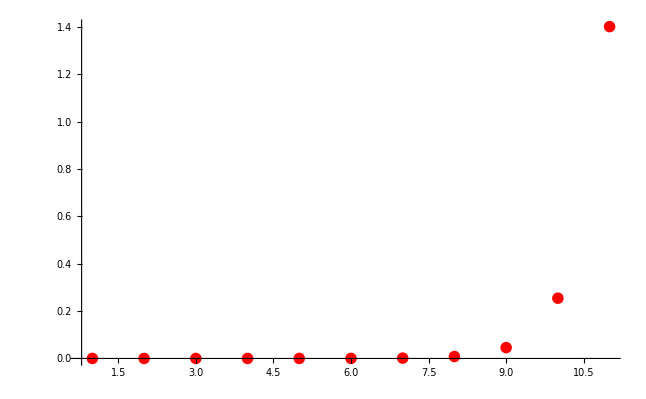

```mathematica
Show[
{
ListPlot[errorarray,PlotRange->All,PlotStyle-> Red]
}
]
```

```mathematica
iarray = ConstantArray[0,21];
iarray[[21]] =0.03125;
errorarray2 = ConstantArray[0,21];
For[n=20,n≥7,n-=1,
t= n+1;
iarray[[t-1]]=1/5*(n^-1-iarray[[t]]); 
temp = N[Integrate[x^t/(x+5),{x,0,1}]];
errorarray2[[t-1]]=Abs[ temp-iarray[[t-1]]]/temp
]
```

Power::infy: 碰到无穷表达式 1/0..

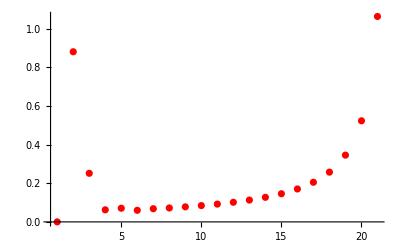

```mathematica
ListPlot[Reverse[errorarray2],PlotRange->All,PlotStyle-> Red]
```

```mathematica
N[Integrate[x^20/(x+5),{x,0,1}]]
```

0.03125

```mathematica
errorarray2
```

{2.14137,1.04902,0.691785,0.515322,0.410338,0.340784,0.291342,0.254402,0.22576,0.202905,0.184247,0.168748,0.15549,0.145175,0.132328,0.133222,0.0171941,0.171949,0.687158,ComplexInfinity,0}

```mathematica
errorarray2
```

{0,0,0,0,0,0,0.291342,0.254402,0.22576,0.202905,0.184247,0.168748,0.15549,0.145175,0.132328,0.133222,0.0171941,0.171949,0.687158,ComplexInfinity,0}

```mathematica
N[Integrate[x^19/(x+5),{x,0,1}]]
```

0.0078125